1.

1.

1.

«19 more identical outputs»

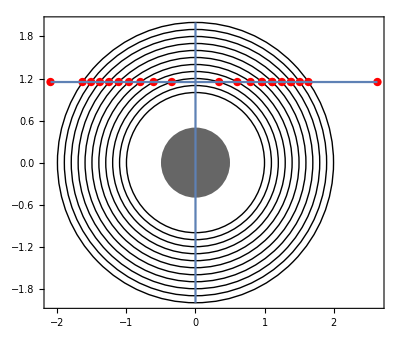

```mathematica
Clear["Global`*"];

(* Assumptions:
 shells are located around the origin
light rays never bend more than 90 degrees
*)

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value *)
(* more will be added to shells as we get into physical properties *)
Shell[r_,n_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n}; 
Ray[point_,θ_]:=y-point[[2]]==Tan[θ] (x-point[[1]]);
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]];
IsPointReal[point_]:=(x/.point)∈Reals&&( y/.point)∈Reals;

SnellsLaw[θin_,nin_,nout_]:=ArcSin[Sin[θin]nin/nout];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_]:=Module[{r,center,nMax,nStep,n},
atmosphere={};

(* TODO - filling in dummy n values for now- probably make a function to pull from actually state variables to calculate n values later *)
nMax = 1.;
nStep = (nMax-1.)/((max-min)/step);
n = nMax;
Do[
{
atmosphere =Append[atmosphere,Shell[r,n]];
n-=nStep;
},
{r,min,max,step}
];
]

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{atmosphere[[i,1]]}],{i,1,Length[atm]}];
MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

(* return only real positive time values *)
tList=Select[{t1,t2},(#∈Reals&&#>0)&]
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius},
{
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
If[Abs[posRadius-shellRadii[[i]]]<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
]
};
rayLocation
]

(* updates the light position based on current position, direction, and shells *)
(* TODO - need to handle the case where it's at the end of the last atmosphere layer *)
MoveLightRay[rayPath_,rayAngle_,atm_]:=Module[{direction,checkShellNum,closestIntersect,sol,location,tList,intersect,t,n2},
position = Last[rayPath];
posRadius = Norm[position];

location  = LocateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]];
shell = Last[atm];
},

(* only need to check the innermost shell *)

location == "inside",
{
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[-2,3]],position,rayAngle]];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle]
]
],

(* if on some other shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)
(* non-intersection case *)
If[t==Infinity,
t = 1, (* just set t to some small value (probably adjust to fit window size later *)
{}
];

intersect = {t+position[[1]],Tan[rayAngle ] t + position[[2]]};

position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
(* get the refractivity of the shell *)
n2 = atm[[i,4]];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 *)
n2 = 1.0
];,
{i,Length[atm]}
];

AppendTo[intersectionPoints,position];
AppendTo[angleList,Refract[intersectionPoints,angleList,n2]]; 

position
]

(* refract based on entry and shell conditions using Snell's Law *)
Refract[rayPath_,angles_,n2_]:=Module[{newAngle,position,prevPosition},
position = Last[rayPath];
prevPosition = rayPath[[-2]];

angle = Last[angles];
Which[
(* need to handle grazing case earlier *)

(* hitting shell from outside in (radius decreasing) *)
Norm[position]<Norm[prevPosition],

(* TODO - this should be okay now- though the other conditions still need to be tested *)
(* TODO - Snell's Law needs to be applied according to which shell we're interacting with *)
newAngle = NormalAngle[position]-π+SnellsLaw[(π-NormalAngle[position]+angle),currentN,n2],

(* hitting shell from inside out *)
(* TODO - check this condition *)
(Norm[position]>Norm[prevPosition]) || (Norm[position]== Norm[prevPosition]),
(*position[[1]]>0,*)
newAngle = NormalAngle[position]-SnellsLaw[(π-NormalAngle[position]-angle),currentN,n2],

(* hitting the top or bottom of a shell- could be either outside-in or inside-out *)
(* TODO *)
position [[1]]== 0,
{
Which[
angle≠ 0,
{
Print["hit top of shell"],
newAngle = Return[π/2-Abs[angle]],
}
angle == 0,
Print["non-intersection case"]
(*TODO non-intersecting grazing case *)

]
}
];
currentN=n2;
newAngle
]

(*run the program starting here *)
TOL = 10^-9;
origin = {-2.1,1.15}; (* origin needs to be specified by doubles rather than ints *)
angle = 0;
currentN = 1.0;

(* TODO can i just get rid of this? *)
lightRay = Ray[origin,angle];

(* TODO - standardize these names *)
intersectionPoints = {origin};
angleList = {angle};
atmMin = 1;
atmMax = 2;
MakeAtmosphere[atmMin,atmMax,0.1];
(* main loop starts here *)
While[Last[intersectionPoints][[1]]< atmMax,
MoveLightRay[intersectionPoints,Last[angleList],atmosphere];
];
(*
Do[
{
AppendTo[intersectionPoints,MoveLightRay[intersectionPoints,Last[angleList],atmosphere]];
AppendTo[angleList,Refract[intersectionPoints,angleList]];
},
{i,1,12}
]
*)

(* graphics stuff starts here *)
PlutoGraphic = Graphics[{GrayLevel[0.4],Disk[{0,0},0.5]}];
Show[PlutoGraphic,MakeAtmosphereGraphic[atmosphere],Graphics[{Red,PointSize[0.015],Point[intersectionPoints]}],ListLinePlot[intersectionPoints],ListLinePlot[{{0,2},{0,-2}}],Frame-> True]
```